```mathematica
(*h=dm2/(4*energy)*{{-Cos[2*theta],Sin[2*theta]},{Sin[2*theta],Cos[2*theta]}};*)
h=dm2/(4*energy)*{{-Cos[2*theta]+A,Sin[2*theta]},{Sin[2*theta],Cos[2*theta]-A}};
eigenVectors=Eigenvectors[h]
eigenVectors[[1]][[1]]*eigenVectors[[2]][[1]]//Simplify;
Eigenvalues[h]
h//MatrixForm;
tan=eigenVectors[[2]][[1]];
cot=-eigenVectors[[1]][[1]];
tan+cot//Simplify
(*2*tan/(1+tan^2)//Expand//Simplify*)
```

{{-Cot[2 theta]+A Csc[2 theta]-√(1+A^2-2 A Cos[2 theta]) Csc[2 theta],1},{-Cot[2 theta]+A Csc[2 theta]+√(1+A^2-2 A Cos[2 theta]) Csc[2 theta],1}}

{-(dm2 √(1+A^2-2 A Cos[2 theta]))/(4 energy),(dm2 √(1+A^2-2 A Cos[2 theta]))/(4 energy)}

√(1+A^2-2 A Cos[2 theta]) Csc[theta] Sec[theta]

```mathematica
$Assumptions=Element[theta12,Reals]&&Element[theta13,Reals]&&Element[theta23,Reals]&&Element[delta,Reals];

omega12={{Cos[theta12],Sin[theta12],0},{-Sin[theta12],Cos[theta12],0},{0,0,1}};
omega13={{Cos[theta13],0,Exp[-I*delta]*Sin[theta13]},{0,1,0},{-Exp[I*delta]*Sin[theta13],0,Cos[theta13]}};
omega23={{1,0,0},{0,Cos[theta23],Sin[theta23]},{0,-Sin[theta23],Cos[theta23]}};
omega12//MatrixForm;
omega13//MatrixForm;
omega23//MatrixForm;
u=omega23.omega13.omega12;
u//MatrixForm;

ds={{Subscript[Δ, 11],Subscript[Δ, 12],Subscript[Δ, 13]},{Subscript[Δ, 21],Subscript[Δ, 22],Subscript[Δ, 23]},{Subscript[Δ, 31],Subscript[Δ, 32],Subscript[Δ, 33]}};

getProbability[alpha_,beta_]:=Module[{re,im,uuuu},
re=0;
im=0;
For[j=1,j<4,j++,
For[i=j+1,i<4,i++,
uuuu=u[[alpha]][[i]]*Conjugate[u[[beta]][[i]]]*Conjugate[u[[alpha]][[j]]]*u[[beta]][[j]]//ComplexExpand;
re=re+Re[uuuu]*Sin[ds[[i,j]]]^2;
im=im+Im[uuuu]*Sin[ds[[i,j]]*2];
]
];
(*re=Simplify[re];*)
(*im=Simplify[im];*)
KroneckerDelta[alpha,beta]-4*re+2*im
]
(*$Assumptions=True;*)
```

```mathematica
prob=Expand[Simplify[getProbability[2,1]]]
```

1/4 Cos[theta13]^2 Cos[delta-2 Δ_21] Sin[2 theta12] Sin[theta13] Sin[2 theta23]-1/4 Cos[theta13]^2 Cos[delta+2 Δ_21] Sin[2 theta12] Sin[theta13] Sin[2 theta23]-1/2 Cos[theta13]^2 Cos[delta-2 Δ_31] Sin[2 theta12] Sin[theta13] Sin[2 theta23]+1/2 Cos[theta13]^2 Cos[delta-2 Δ_32] Sin[2 theta12] Sin[theta13] Sin[2 theta23]-1/4 Cos[theta12] Cos[theta13]^2 Cos[2 (theta13+theta23)] Sin[theta12] Sin[2 theta12] Sin[Δ_21]^2+1/4 Cos[theta13]^2 Sin[2 theta12]^2 Sin[Δ_21]^2+1/4 Cos[theta13]^2 Cos[2 theta13] Sin[2 theta12]^2 Sin[Δ_21]^2-1/8 Cos[theta13]^2 Cos[2 theta13-2 theta23] Sin[2 theta12]^2 Sin[Δ_21]^2+3/4 Cos[theta13]^2 Cos[2 theta23] Sin[2 theta12]^2 Sin[Δ_21]^2+1/2 Cos[delta] Cos[theta13]^2 Sin[4 theta12] Sin[theta13] Sin[2 theta23] Sin[Δ_21]^2+4 Cos[theta12]^2 Cos[theta13]^2 Sin[theta13]^2 Sin[theta23]^2 Sin[Δ_31]^2+4 Cos[theta13]^2 Sin[theta12]^2 Sin[theta13]^2 Sin[theta23]^2 Sin[Δ_32]^2

```mathematica
Select[Expand[prob],!FreeQ[#,Subscript[Δ, 31]]&]//Simplify;
Select[Expand[prob],MemberQ[#,Sin[Subscript[Δ, 31]]^2]&]//Simplify;
Select[Expand[prob],MemberQ[#,Sin[theta13]]&]
```

1/4 Cos[theta13]^2 Cos[delta-2 Δ_21] Sin[2 theta12] Sin[theta13] Sin[2 theta23]-1/4 Cos[theta13]^2 Cos[delta+2 Δ_21] Sin[2 theta12] Sin[theta13] Sin[2 theta23]-1/2 Cos[theta13]^2 Cos[delta-2 Δ_31] Sin[2 theta12] Sin[theta13] Sin[2 theta23]+1/2 Cos[theta13]^2 Cos[delta-2 Δ_32] Sin[2 theta12] Sin[theta13] Sin[2 theta23]+1/2 Cos[delta] Cos[theta13]^2 Sin[4 theta12] Sin[theta13] Sin[2 theta23] Sin[Δ_21]^2

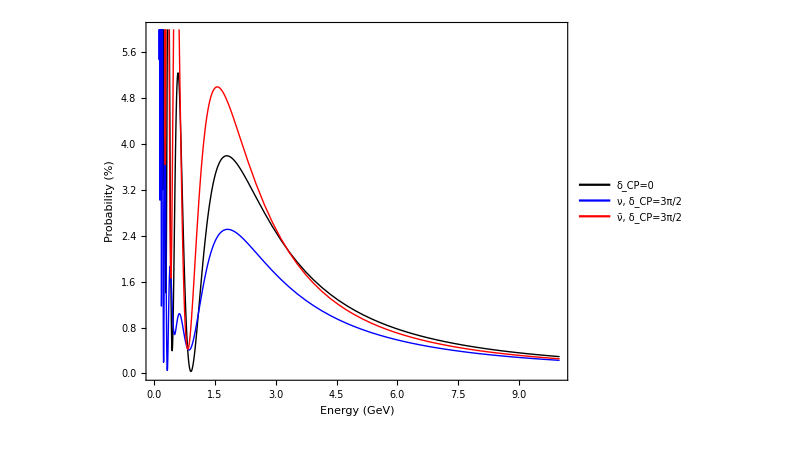

```mathematica
baseline=810;(*km*)
dm221=7.56*10^(-5);(*eV2*)
dm231=2.55*10^(-3);(*eV2*)
dm232=dm231-dm221;(*eV2*)
energy=2.;(*GeV*)
Clear[energy];
values={
theta13->8.41*Degree,
theta12->34.5*Degree,
theta23->41.*Degree,
(*delta->252.*Degree,*)
Subscript[Δ, 21]->dm221*1.27*baseline/energy,
Subscript[Δ, 31]->dm231*1.27*baseline/energy,
Subscript[Δ, 32]->dm232*1.27*baseline/energy
};
probability=getProbability[2,1];
probCp0[x_]:=probability/.values/.energy->x/.delta->0;
probCp3PiOver2[x_]:=probability/.values/.energy->x/.delta->3*Pi/2;
probCpMinus3PiOver2[x_]:=probability/.values/.energy->x/.delta->-3*Pi/2;
(*probCp3PiOver2[2.]*)
(*probCp0[2.]*)

plot=Plot[
{
probCp0[x]*100,
probCp3PiOver2[x]*100,
probCpMinus3PiOver2[x]*100
},
{x,0.1,10},
PlotLegends->Placed[LineLegend[{"δ_CP=0","ν, δ_CP=3π/2","ν̄, δ_CP=3π/2"},LegendMarkerSize->40],{0.75,0.75}],
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Red,Thick]},
PlotRange->{{0,10},{0,6}}
(*AxesOrigin->{0,0}*)
];
Show[plot,
(*AxesLabel->{"Energy (GeV)", "Probability (%)"},*)
ImageSize->600,
AspectRatio->600/800,
(*ImageMargins->50,*)
BaseStyle->{FontSize->20},
Frame->True,
FrameLabel->{{"Probability (%)",None},{"Energy (GeV)",None}},
(*Axes->True,*)
(*AxesOrigin->{5,50}*)
(*TicksStyle->Thick,*)
FrameStyle->Directive[Black,Thick]
]
```

```mathematica
u[[2,3]]
u[[1,3]]
u[[2,2]]
u[[1,2]]
```

Cos[theta13] Sin[theta23]

ⅇ^(-ⅈ delta) Sin[theta13]

Cos[theta12] Cos[theta23]-ⅇ^(ⅈ delta) Sin[theta12] Sin[theta13] Sin[theta23]

Cos[theta13] Sin[theta12]

```mathematica
ArcSin[0.028^0.5]/Degree
```

9.63273

```mathematica
Sin[9.63*2*Degree]
```

0.329855

```mathematica
values={
theta13->8.41*Degree,
theta12->34.5*Degree,
theta23->41.*Degree
};
Cos[theta12]*Cos[theta23]/.values
Sin[theta12]*Sin[theta13]*Sin[theta23]/.values
Sin[theta12]/.values
Sin[theta13]/.values
Sin[theta23]/.values
```

0.621976

0.054348

0.566406

0.146256

0.656059

```mathematica
(*getProbability[2,2]/.Sin[theta13]->0/.Sin[Subscript[Δ, 21]]->0//Simplify*)
prob=getProbability[2,2]/.Sin[Subscript[Δ, 21]]->0/.Sin[Subscript[Δ, 31]]->Sin[Subscript[Δ, 32]]//Simplify;
prob//TraditionalForm
(*prob[[1]]+prob[[2]]+prob[[4]]/.Sin[theta13]->0//Simplify*)
(*prob[[1]]+prob[[2]]+prob[[4]]//Simplify*)
(*prob=Expand[Simplify[getProbability[2,2]]]*)
```

sin^2(Δ_32) (-sin^2(theta12)) sin^2(2 theta13) sin^4(theta23)-4 sin^2(Δ_32) sin^2(theta12) cos^2(theta13) sin^2(theta23) cos^2(theta23)-4 sin^2(Δ_32) cos^2(theta12) cos^2(theta13) sin^2(theta23) (sin^2(theta13) sin^2(theta23)+cos^2(theta23))+1